```mathematica
ME314 Final Project;
FeiyuChen;
Scene2;
```

```mathematica
Quit[]
```

```mathematica
(*Open and run all other Mathematica scripts*)
myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["../funcs_math.nb"];
myOpenFile["../funcs_assist.nb"];
myOpenFile["../funcs_main.nb"];
(* !!!!!!!!! wait for 1 second before running the following !!!!!)
```

```mathematica
CreateObjects:=Module[{},


(* Object 1: What is this object? I don't know. *)
nthGroup=1;
initRandVelocity=0.3;

l=0.4;
lExtend=0.4;

NumOfEdges=3;(* create a strainge *)
oriPoint=Trans4[0,-0.8];
createVertex[oriPoint];
linki=createLink1DOFgθl[oriPoint,-Pi/2,l/2];
linki=createLink0DOFgθl[linki[[IdxTFront]],+Pi/2,l/2];
linkExtend=createLink0DOFgθl[linki[[IdxTFront]],0,lExtend];
For[i=1,i≤NumOfEdges-1,i=i+1,
linki=createLink0DOFgθl[linki[[IdxTFront]],2*Pi/NumOfEdges,l];
linkExtend=createLink0DOFgθl[linki[[IdxTFront]],0,lExtend];
];


NumOfEdges=2;(* attach two links *)
linki=createLink1DOFgθl[linki[[IdxTFront]],+Pi/2,l];
For[i=1,i≤NumOfEdges-1,i=i+1,
linki=createLink1DOFgθl[linki[[IdxTFront]],2*Pi/NumOfEdges,l]
];

(* Objects 3: Wall of Floor *)
nthGroup=3;
wally=-1.8;
wallx=1;
createLink0DOFpp[{-wallx,wally},{+wallx,wally}];
createLink0DOFpp[{-wallx,wally},{-wallx,-0.3}];
createLink0DOFpp[{+wallx,wally},{+wallx,-0.3}];
];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

externalForces=ConstantArray[0,nVars];

Print["\nStart Solving ..."];
mainSolveELeqs;
Print["Finish Solving ..."];

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

Print["\nStart setting impact ..."];
SetUpImpacts[];
Print["Finish setting impact ..."];
```

Start Solving ...

Finish Solving ...

Start setting impact ...

Finish setting impact ...

```mathematica
(* Set up params for NDSolve *)
SetUpImpactEvents
timeend=5;(* total simulation time *)
MAXIMPACTTIMES=3;
impactDetectionError=0.05;
intergrationMaxStepSize=0.01;
ifprint=True;
```

```mathematica
(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];
```

Computing simulation: 2.62536 / 5 ...

Impact at: t=2.62536,impactcase=28

Before reflection, q={-1.13579+0. ⅈ,0.40819+0. ⅈ,6.44326+0. ⅈ}
                      dq={-0.266677+0. ⅈ,-3.19466+0. ⅈ,0.741996+0. ⅈ}

After reflection, dq:{-1.11209,0.766409,4.93167}

Computing simulation: 4.36489 / 5 ...

Impact at: t=4.36489,impactcase=28

Before reflection, q={-1.36489+0. ⅈ,0.206445+0. ⅈ,12.3162+0. ⅈ}
                      dq={0.908416+0. ⅈ,-0.848337+0. ⅈ,4.68486+0. ⅈ}

After reflection, dq:{-0.512637,-0.122699,-4.36241}

Not an impact

Computing simulation is completed.

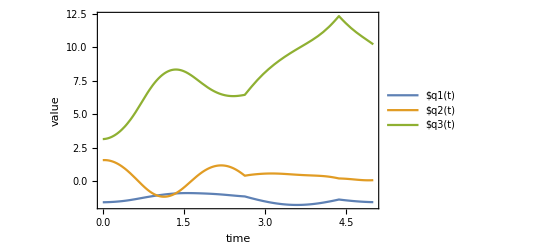

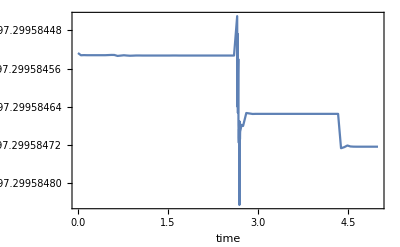

```mathematica
(* Plot *)
plotVariablesValues
plotHamValues
plotAnimation[{{-2,2},{-2,0}}]
```